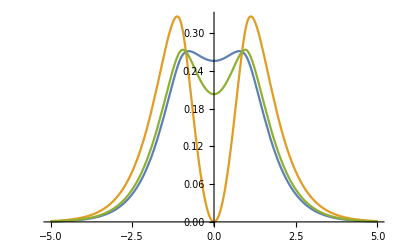

```mathematica
Get["MaTeX`"]
A[z_,r_]:=1/Sqrt[Pi] Exp[-Sqrt[(z-1)^2+r^2]]
B[z_,r_]:=1/Sqrt[Pi] Exp[-Sqrt[(z+1)^2+r^2]]
p1[z_]:=1/(2+26/(3 E^2))2Pi NIntegrate[(A[z,r]+B[z,r])^2 r,{r,0,+Infinity}]
p2[z_]:=1/(2-26/(3 E^2))2Pi NIntegrate[(A[z,r]-B[z,r])^2 r,{r,0,+Infinity}]
p3[z_]:=1/2 2Pi NIntegrate[(A[z,r]^2+B[z,r]^2)r,{r,0,+Infinity}]
Plot[{p1[z],p2[z],p3[z]},{z,-5,5},
AxesLabel->{MaTeX["z"],MaTeX["\\rho"]},
PlotLegends->{MaTeX["\\rho_+"],MaTeX["\\rho_-"],MaTeX["\\rho"]},
LabelStyle->Directive[FontFamily->"CMU Serif",FontSize->10.5]]
```